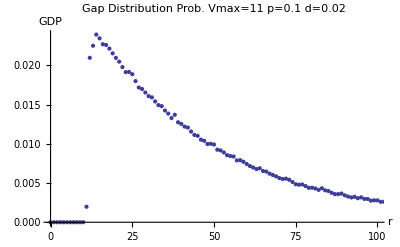

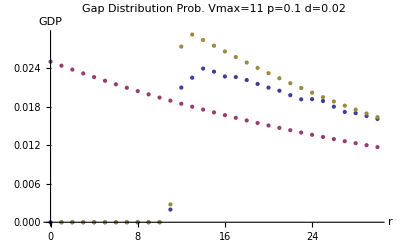

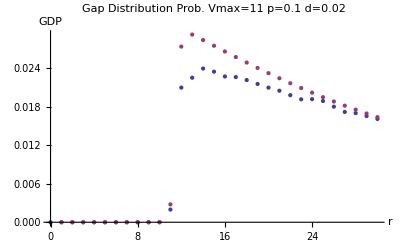

```mathematica
d="0.02";
dd=0.02;
ddd=1/(1/dd-10);
p="0.1";
vmax="11";
gap="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/GapD.d.";
AN1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d"<>d<>"-1.txt",{Number,Number}];
AN2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d"<>d<>"-2nd.txt",{Number,Number}];
g1=".p"<>p<>".v11.txt";
gapadd=gap<>d<>g1;
gapd=ReadList[gapadd,{Number,Number}];
random=Table[{i,(1-ddd)^i*ddd},{i,0,10/ddd}];
g=gapd[[All,2]];
ag=AN[[All,2]];
an1=AN1[[All,2]];
an2=AN2[[All,2]];
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,100},Full}]

ListPlot[{gapd,random,AN2},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,30},Full}]
ListPlot[{gapd,AN2},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,30},Full}]
```

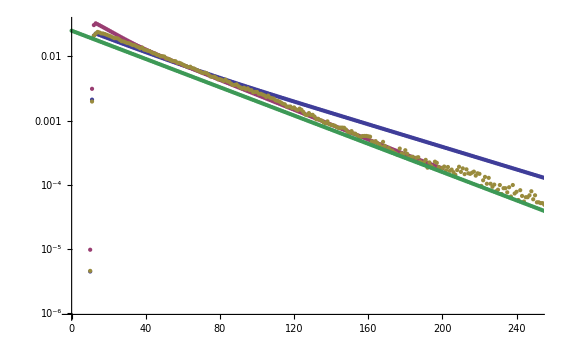

```mathematica
ListLogPlot[{AN1,AN2,gapd,random},PlotRange->{{0,250},Full}]
```

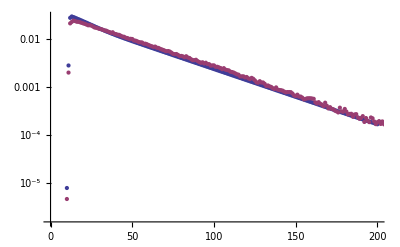

```mathematica
ListLogPlot[{AN2,gapd},PlotRange->{{0,200},Full}]
```

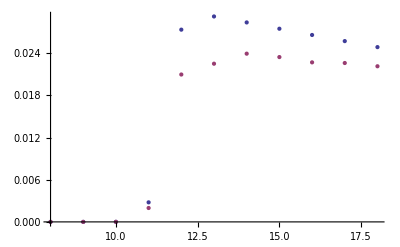

```mathematica
ListPlot[{AN2,gapd},PlotRange->{{8,18},Full}]
```

```mathematica
Sum[AN2[[All,2]][[i]],{i,1,200}]
Sum[gapd[[All,2]][[i]],{i,1,201}]
```

0.993174

0.99229

```mathematica
0.9931743179700001/0.9922904001599995
```

```mathematica
1.0008907854090476*1.41421
```

1.41547

```mathematica
(1-0.025)^250*0.025
```

```mathematica
0.000044575264955864824/0.025
```

0.00178301

```mathematica
0.9922904001599995+0.001783010598234593
```

0.994073

```mathematica
AN2[[120]]
gapd[[121]]
```

{120,0.00137264}

{120,0.00159939}

```mathematica
0.00159939/0.00137264
```

1.16519

```mathematica
AN2
gapd
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,4.02309×10^-8},{9,0.0000117561},{10,0.00342255},{11,0.0334458},{12,0.0355023},{13,0.0341559},{14,0.0328421},{15,0.0315623},{16,0.030318},{17,0.0291105},{18,0.0279413},{19,0.0268117},{20,0.0257228},{21,0.0246756},{22,0.0236707},{23,0.0227086},{24,0.0217894},{25,0.020913},{26,0.0200789},{27,0.0192866},{28,0.018535},{29,0.0178229},{30,0.0171491},{31,0.0165119},{32,0.0159097},{33,0.0153407},{34,0.014803},{35,0.0142948},{36,0.0138142},{37,0.0133592},{38,0.0129282},{39,0.0125192},{40,0.0121307},{41,0.011761},{42,0.0114086},{43,0.0110722},{44,0.0107505},{45,0.0104422},{46,0.0101464},{47,0.00986202},{48,0.00958827},{49,0.00932436},{50,0.00906958},{51,0.00882334},{52,0.00858508},{53,0.00835432},{54,0.00813064},{55,0.00791366},{56,0.00770305},{57,0.00749849},{58,0.00729974},{59,0.00710655},{60,0.00691869},{61,0.00673598},{62,0.00655824},{63,0.00638529},{64,0.00621698},{65,0.00605317},{66,0.00589373},{67,0.00573852},{68,0.00558743},{69,0.00544033},{70,0.00529712},{71,0.00515769},{72,0.00502194},{73,0.00488977},{74,0.00476108},{75,0.00463578},{76,0.00451378},{77,0.00439499},{78,0.00427933},{79,0.00416672},{80,0.00405707},{81,0.0039503},{82,0.00384634},{83,0.00374512},{84,0.00364657},{85,0.00355061},{86,0.00345717},{87,0.00336619},{88,0.00327761},{89,0.00319135},{90,0.00310737},{91,0.0030256},{92,0.00294598},{93,0.00286845},{94,0.00279297},{95,0.00271947},{96,0.00264791},{97,0.00257823},{98,0.00251038},{99,0.00244433},{100,0.00238001},{101,0.00231738},{102,0.00225641},{103,0.00219704},{104,0.00213923},{105,0.00208296},{106,0.00202816},{107,0.00197482},{108,0.00192288},{109,0.00187232},{110,0.00182309},{111,0.00177518},{112,0.00172853},{113,0.00168313},{114,0.00163895},{115,0.00159594},{116,0.00155409},{117,0.00151338},{118,0.00147376},{119,0.00143522},{120,0.00139774},{121,0.0013613},{122,0.00132587},{123,0.00129143},{124,0.00125796},{125,0.00122545},{126,0.00119388},{127,0.00116323},{128,0.00113349},{129,0.00110464},{130,0.00107667},{131,0.00104956},{132,0.00102331},{133,0.00099789},{134,0.0009733},{135,0.000949524},{136,0.000926551},{137,0.000904367},{138,0.000882962},{139,0.000862323},{140,0.000842437},{141,0.000823292},{142,0.000804875},{143,0.000787174},{144,0.000770173},{145,0.00075386},{146,0.000738236},{147,0.000718808},{148,0.000699892},{149,0.000681474}}

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,4.58716×10^-6},{11,0.00197706},{12,0.0209633},{13,0.0225},{14,0.0239266},{15,0.0234434},«16352»,{16368,0},{16369,0},{16370,0},{16371,0},{16372,0},{16373,0},{16374,0},{16375,0},{16376,0},{16377,0},{16378,0},{16379,0},{16380,0},{16381,0},{16382,0},{16383,0}}

```mathematica
0.00915749/0.00874578
```

```mathematica
1.047075275161278*1.4142135623730951/1.4340339736839016
```

1.0326

```mathematica
{5,0.0100061}
```

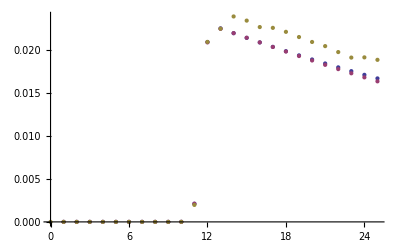

```mathematica
ListPlot[{AN1,AN2,gapd},PlotRange->{{0,25},Full}]
```

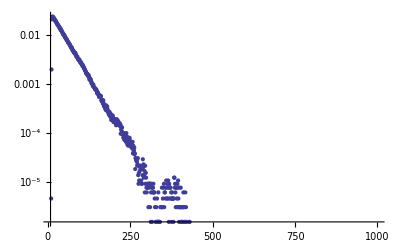

```mathematica
ListLogPlot[{gapd},PlotRange->{{8,1000},Full}]
```

```mathematica
gapd[[250]]
gapd[[249]]
gapd[[248]]
```

{249,0.000059633}

{248,0.0000795107}

```mathematica
{247,0.0000688073}
```

{247,0.0000688073}

```mathematica
m=11;

ClearAll[g,p];
v1[m-2][3]=p;
v1[m-2][2]=1-p;
v1[m-2][1]=0;
v1[m-2][0]=0;

v1[m-1][3]=0;
v1[m-1][2]=p;
v1[m-1][1]=1-p;
v1[m-1][0]=0;

v1[m][3]=0;
v1[m][2]=0;
v1[m][1]=p;
v1[m][0]=1-p;


v1[m+1][3]=0;
v1[m+1][2]=0;
v1[m+1][1]=p;
v1[m+1][0]=1-p;


v2[0]=g[m-2]*v1[m-2][0]+g[m-1]*v1[m-1][0]+g[m]*v1[m][0]+g[m+1]*v1[m+1][0]+(1-g[m-2]-g[m-1]-g[m]-g[m+1])*(1-p);
v2[1]=g[m-2]*v1[m-2][1]+g[m-1]*v1[m-1][1]+g[m]*v1[m][1]+g[m+1]*v1[m+1][1]+(1-g[m-2]-g[m-1]-g[m]-g[m+1])*p;
v2[2]=g[m-2]*v1[m-2][2]+g[m-1]*v1[m-1][2]+g[m]*v1[m][2]+g[m+1]*v1[m+1][2];
v2[3]=g[m-2]*v1[m-2][3]+g[m-1]*v1[m-1][3]+g[m]*v1[m][3]+g[m+1]*v1[m+1][3];
```

```mathematica
Simplify[v2[0]]
```

(-1+p) (-1+g[9]+g[10])

```mathematica
v1[11][0]
```

0.9